```mathematica
DataStatistic[x_List]:=Module[{mean,tValue=1.14,deltaB=0.0095,uncertainty},MeanStandardDeviation[data_]:=StandardDeviation[data]/Sqrt[Length[data]];
DeltaA[data_,t_]:=t*StandardDeviation[data];
Uncertainty[data_,t_,deltaB_]:=Sqrt[DeltaA[data,t]^2+deltaB^2];mean=Mean[x];
uncertainty=Uncertainty[x,tValue,deltaB];
Print["Mean: ",mean];
Print["Standard Deviation: ",StandardDeviation[x]];
Print["Mean Standard Deviation: ",MeanStandardDeviation[x]];
Print["deltaA: ",DeltaA[x,tValue]];Print["deltaB: ",deltaB];
Print["Uncertainty: ",uncertainty];
Return[Around[mean,uncertainty]]];
ShowFitPlot[dataX_List,dataY_List,xName_,yName_,plotName_]:=Module[{data,fitModel},data=Transpose[{dataX,dataY}];
fitModel=LinearModelFit[data,x,x];
Print["Best Fit Equation: ",fitModel["BestFit"]];
Print[Show[ListPlot[data,PlotStyle->Red,PlotLabel->plotName,AxesLabel->{xName,yName}],Plot[fitModel[x],{x,Min[dataX],Max[dataX]}]]];
Return[fitModel["BestFitParameters"][[2]]]];
ShowFitPlot[dataX_List,dataY_List,xName_,yName_]:=ShowFitPlot[dataX,dataY,xName,yName,""];
ShowFitPlot[dataX_List,dataY_List]:=ShowFitPlot[dataX,dataY,"","",""];
```

Mean: 35.

Standard Deviation: 0.0141421

Mean Standard Deviation: 0.00632456

deltaA: 0.016122

deltaB: 0.0095

Uncertainty: 0.0187128

35.0000.019

Mean: 33.

Standard Deviation: 0.0141421

Mean Standard Deviation: 0.00632456

deltaA: 0.016122

deltaB: 0.0095

Uncertainty: 0.0187128

33.0000.019

Best Fit Equation: 0.216667+2.80906 x

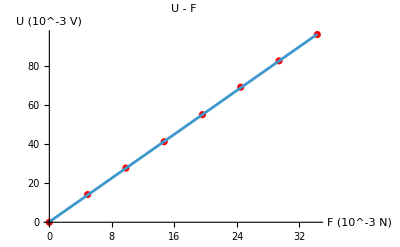

2.80906

Mean: 43.6333

Standard Deviation: 0.273252

Mean Standard Deviation: 0.111555

deltaA: 0.311507

deltaB: 0.0095

Uncertainty: 0.311652

43.630.31

15.530.11

0.07270.0005

```mathematica
dataD1={35.00,35.02,35.00,35.00,34.98};
dataD2={33.00,33.00,33.02,32.98,33.00};

D1=DataStatistic[dataD1]
D2=DataStatistic[dataD2]

dataM=Table[i,{i,0,3.5,0.5}];
dataU={0,14.2,27.8,41.3,55.2,69.3,82.8,96.3};
dataF=dataM*9.794;
B=ShowFitPlot[dataF,dataU,"F (10^-3 N)","U (10^-3 V)","U - F"]

datadeltaU={43.4,43.8,43.9,43.2,43.7,43.8};
deltaU=DataStatistic[datadeltaU]

f=deltaU/B
α=f/(Pi (D1+D2))
```